```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

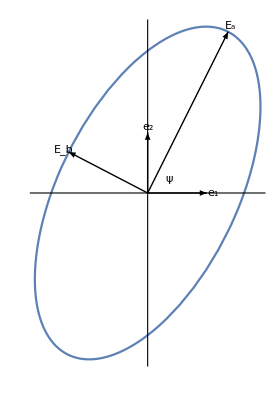

```mathematica
ClearAll[p1, bold, ellipse]

bold = Style[ #, Bold] &;

ellipse[a_, b_, psi_,phi_] := Module[{e,mu,f},
e = Sqrt[1 - (b/a)^2];
mu = ArcTanh[ b/a ];
f = e a Exp[I psi] Cosh[ mu + I phi] ;
{f//Re,f//Im}
]

p1 =Module[{psi,a,b,te1, te2, e1, e2, o, va, vb, ea,eb},
psi = 0.35 Pi;
o = {0,0};
a = 3;
b = 1.5;
va = ellipse[a,b,psi,0];
vb = ellipse[a,b,psi,Pi/2];
{e1,e2} = IdentityMatrix[2];
te1 = Subscript["e"// bold, 1];
te2 = Subscript["e"// bold, 2];
ea = Subscript["E"// bold, "a"];
eb = Subscript["E"// bold, "b"];
Show[
{
Graphics[
ParametricPlot[ellipse[a,b,psi, t],{t,0,2 Pi}, Ticks  -> None]
, AspectRatio-> 1
]
,
Graphics[{
Arrow[{o, e1}],
Arrow[{o, e2}],
Text[te1, 1.1 e1],
Text[te2, 1.1 e2],
Arrow[{o,va}],
Arrow[{o,vb}],
Text[ea, va + .1(va//Normalize)],
Text[eb, vb + .1(vb//Normalize)],
Text[ "ψ", ellipse[a,b,psi/2,0]/7]

}
,BaseStyle->14 
]
}]

]
```

```mathematica
peeters`exportForLatex["ellipticalPolarizationFig1", p1]
```